## First define the genrator base

```mathematica
allGeneratorVariables=Sort[Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs4[k,"graph"]]]},
allGraphs4[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs4GeneratorAtomKeys}
],CompareSymbols];
```

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs4[k,"colofourgenerator"]==allGraphs4[k,"colofour"]
,
{k,allGraphs4GeneratorAtomKeys}
],
Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs4[k,"colofourgenerator"]=Simplify[allGraphs4[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs4]]}
],k];
```

## Now define the base basic data

```mathematica
Bases=Association[];
```

```mathematica
Bases["C"]=Association[];
```

```mathematica
Bases["C","Colofour"]="colofour";
```

```mathematica
Bases["E"]=Association[];
```

```mathematica
Bases["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases["G"]=Association[];
```

```mathematica
Bases["G","Colofour"]="colofourgenerator";
```

```mathematica
allBases={"C","E","G"}
```

{C,E,G}

## Compute keys and variables

```mathematica
Table[Bases[base,"AtomKeys"]=Sort[Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,Bases[base,"Colofour"]]]]==1&],CompareSymbols[allGraphs4[#1,Bases[base,"Colofour"]],allGraphs4[#2,Bases[base,"Colofour"]]]&]
,{base,allBases}];
```

```mathematica
Table[Bases[base,"Variables"]=Table[allGraphs4[k,Bases[base,"Colofour"]],{k,Bases[base,"AtomKeys"]}]
,{base,allBases}];
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs4[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

42

## Checking some conversion matrix identities

```mathematica
ConversionMatrix["E","C"]==Transpose[ConversionMatrix["G","C"]]
```

True

```mathematica
ConversionMatrix["E","C"]==Inverse[ConversionMatrix["C","E"]]
```

True

```mathematica
ConversionMatrix["G","C"]==Transpose[Inverse[ConversionMatrix["C","E"]]]
```

True

```mathematica
Table[base->ConversionMatrix[base,base]==IdentityMatrix[42],{base,allBases}]
```

{C→False,E→False,G→False}

## Viewing come COnversion matrcxes

```mathematica
Table[Det[ConversionMatrix[base1,base2]],{base1,allBases},{base2,allBases}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
Table[base1->Eigenvalues[ConversionMatrix[base1,base2]]//N,{base1,allBases},{base2,{"G"}}]
```

{{C→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{E→{0.+2.80588 ⅈ,0.-2.80588 ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,1.,0.+0.356394 ⅈ,0.-0.356394 ⅈ}},{G→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
Table[base1->Det[ConversionMatrix[base1,base2]],{base1,allBases},{base2,{"G"}}]
```

{{C→1},{E→1},{G→1}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs4[k,"vertexsets"]]],{k,allGraphs4AtomKeys}]]
```

{{{1,1,1,1},1},{{1,1,2},6},{{1,3},4},{{2,2},3},{{4},1}}

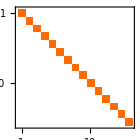
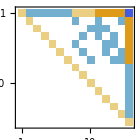
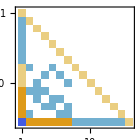
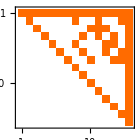
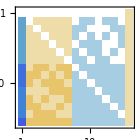
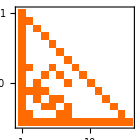
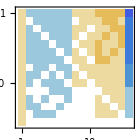
| C | E | G
C | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2],ImageSize->140],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

```mathematica
TableForm[Table[MatrixPlot[Inverse[ConversionMatrix[base1,base2]],ImageSize->140],{base1,allBases},{base2,allBases}],TableHeadings->{Reverse[allBases], Reverse[allBases]},TableAlignments->{Center, Center}]
```

| G | E | C
G | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
C | -Graphics- | -Graphics- | -Graphics-

```mathematica
ConversionMatrix["G","E"].ConversionMatrix["E","C"]==ConversionMatrix["G","C"]
```

True

```mathematica
labels=Table [With[
{k=Bases["E","AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]
```

{1→-Graphics-0,2→-Graphics-2,3→-Graphics-18,4→-Graphics-6,5→-Graphics-486,6→-Graphics-162,7→-Graphics-54,8→-Graphics-488,9→-Graphics-168,10→-Graphics-72,11→-Graphics-26,12→-Graphics-666,13→-Graphics-546,14→-Graphics-218,15→-Graphics-728}

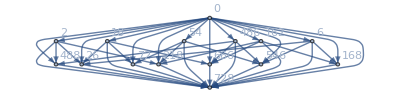
-Graphics-{15,45}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["E","C"]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
Keys[Bases]
```

{C,E,G}

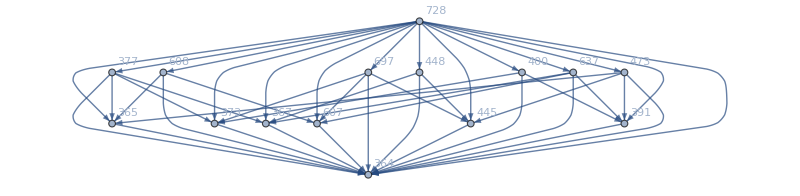
-Graphics-{15,45}

```mathematica
With[
{base1="G",base2="C"},
With[
{labels=Table [With[
{k=Bases[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

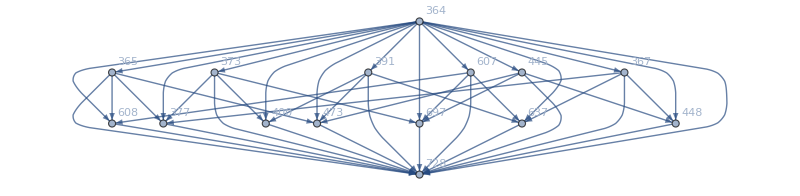
-Graphics-{15,45}

```mathematica
With[
{base1="E",base2="C"},
With[
{labels=Table [With[
{k=Bases[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```